```mathematica
(* Guy F Mongelli                                      ChE 400
Prof. Clark                                           10/25/2010  *)

(* Assignment #7   *)
```

# ME 201/MTH 281/ME400/CHE400 Newton's Law of Cooling

## 1. Introduction

This notebook uses Mathematica to solve the problem presented in class, in section 5.1 of the notes.  The problem is one of transient heat conduction in a slab of finite width L.  The boundary condition on the left face of the slab is zero heat flux, and the condition on the right face of the slab is Newton's law of cooling, with an ambient temperature T_a.  The initial temperature is the function T_0(x).  The relevant material properties are the thermal conductivity k, the thermal diffusivity D_f, and the heat transfer coefficient h, all assumed constant.  The specific expressions for all functions and parameters  are given below in section 2.  The mathematical formulation of the problem is given below.

```mathematica
(*  Notebook was originally coded for  the following problem  *)
```

(∂T)/(∂t) = D_f(∂^2 T)/(∂x^2) , 0<x<L, t>0,

with  (∂T)/(∂x)(0,t) = 0, k(∂T)/(∂x)(L,t) + h[T(L,t) - Ta] = 0,
		
and T(x,0) = T_0(x) .

```mathematica
(* This notebook needs to be altered to solve the following problem ... *)
```

(∂T)/(∂t) = D_f(∂^2 T)/(∂x^2) , 0<x<L, t>0,

with  k(∂T)/(∂x)(0,t) = h[T(0,t)-Ta], k(∂T)/(∂x)(L,t)  = F0,
		
and T(x,0) = T_0(x) .

## 2. Parameter Values

In this section, we define the parameter values and the initial function.  This is the only place in the notebook where these quantities are given specifically.  This makes it possible to change a value for the entire calculation by just changing it here.  The material properties are appropriate for granite.  The initial temperature is taken here to be a constant.

```mathematica
h=22.4;  (** W/m^2·K **)
```

```mathematica
L=0.75;  (** m **)
```

```mathematica
k=16.2;  (** W/m·K **)
```

```mathematica
Df=4.1*10^-6;(** m^2/s **)
```

```mathematica
TA=10.0;  (** °C **)
```

```mathematica
F0=170.2;  (** W/m^2  **)
```

```mathematica
T0[x_]= 10.0; (** °C **)
```

## 3. Steady State Solution

As in other problems of this sort, we must first find the steady-state solution T_s(x), and then reformulate the problem in terms of the transient solution T_r.  The steady-state solution is obtained by setting the time derivative to zero in the original equation for T.  The solution of the resulting equation is a linear function of x, and we require that particular linear function which satisfies the boundary conditions at x = 0 and L.  The result (which is intuitively obvious) is that T_s(x) is constant and equal to the ambient temperature:

```mathematica
Ts[x_]:=F0/k x+F0/h+TA
```

## 4. Formulation of Problem for Transient

Now that we have the steady-state solution, we decompose the full solution into a steady-state part T_s(x) and a transient part T_r(x,t):

T(x,t) = T_s(x) + T_r(x,t)  .

By substituting this decomposition into the original equation for T, we find the following problem for the transient:

(∂T_r)/(∂t) = D_f(∂^2 T_r)/(∂x^2) , 0<x<L, t>0,

with  (∂T_r)/(∂x)(0,t) = 0, k(∂T_r)/(∂x)(L,t) + h T_r(L,t) = 0,
		
and T_r(x,0) = T_0(x)-T_s(x) .

This is the problem that we solve by separation of variables.

## 5. Separation of Variables in Transient Problem

Following the standard approach in separation of variables, we seek functions which satisfy the equation for T_r and the homogeneous boundary conditions at x = 0, L.  We assume a form F(x)G(t) for such solutions.  The two separated equations then have the form

F''(x) + λF(x) = 0,  with   F'(0) = 0   and   kF'(L) + hF(L) = 0, 

and  G'(t) + λDG(t) = 0 .

The general solution for the equation for F(x) is a linear combination of sin(√λx) and cos(√λx).  Applying the two homogeneous boundary conditions to the general solution, we get F(x) = cos(√λx), and simplifying the resulting eigenvalue equation, we get

tan(z) = B_i/z , where z = L √λ, and where B_i = hL/k .

We define the relevant quantities for Mathematica, denoting the nth value of z by z[n], and the nth eigenvalue by lam[n].

```mathematica
lam[n_]:=(z/L)^2/.z->z[n]
```

where the values z[1], z[2], .. z[n],..  are the roots of eig1 = eig2, where

```mathematica
eig1 =Tan[z];
```

```mathematica
eig2=h*L/(k*z);
```

with

```mathematica
Bi:=(h*L)/(k)
```

The generic eigenfunction is

```mathematica
geneig[x_] := Cos[z*(1-x/L)]
```

and the nth eigenfunction is given by

```mathematica
Feig[x_,n_]:=geneig[x]/.z->z[n]
```

The generic normalization integral is

```mathematica
nor = Simplify[Integrate[(geneig[x])^2,{x,0,L}],Element[n,Integers]]
```

0.375+(0.1875 Sin[2. z])/z

and the nth normalization integral is

```mathematica
norm[n_] :=nor/.z->z[n]
```

## 6. Determination of Eigenvalues

We now determine numerically the eigenvalues.  We begin by plotting the expressions eig1 and eig2.  At each crossing of these, there is an eigenvalue.

```mathematica
SetOption[Plot,ImageSize->500];
```

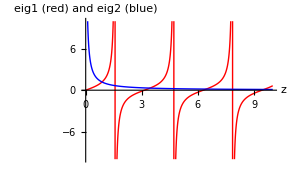

```mathematica
Plot[{eig1,eig2},{z,0,10},PlotRange->{-10,10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"z","eig1 (red)
and eig2 (blue)"},Ticks->{{0,Pi/2,Pi,3 Pi/2,2Pi,5 Pi/2,3Pi}}]
```

We see that the first root is between 0 and π/2, and each subsequent root is in an interval of length π.  It is also clear that for large n, the nth root is very close to (n-1)π.  To find accurate numerical values of the z's, we use the Mathematica command FindRoot.  FindRoot requires an initial guess.  The nth value of z, as we can see from the graph, is between (n - 1)ℼ and (n -0.5 )π.  We take as an initial guess (n - 0.5)π -0.1.  The command is then of the form FindRoot[eig1 == eig2,{z, (n - 0.5)π -0.1}].  We now use this command in a Do loop to calculate and display in a table the first 40 roots.  This will suffice for any calculation requiring up to 40 terms in the eigenfunction series.  We also display the eigenvalue λ, and the approximate value z = (n-1)π.

```mathematica
zroot[n_]:=FindRoot[eig1==eig2,{z,(n-0.5)*Pi-0.1}]
```

```mathematica
zasymp[n_]:=N[(n-1)*Pi]
```

```mathematica
Do[z[n]=z/.zroot[n],{n,1,40}];
```

```mathematica
TableForm[Table[{n,PaddedForm[z[n],{10,4}],PaddedForm[zasymp[n],{10,4}],PaddedForm[lam[n],{10,4}]},{n,1,40}],TableHeadings->{None,{"n","       z[n]","    zasymp[n]","      lam[n]"}}]
```

n |        z[n] |     zasymp[n] |       lam[n]
1 |       0.8718 |       0.0000 |       1.3511
2 |       3.4348 |       3.1416 |      20.9741
3 |       6.4428 |       6.2832 |      73.7945
4 |       9.5331 |       9.4248 |     161.5656
5 |      12.6482 |      12.5664 |     284.4025
6 |      15.7736 |      15.7080 |     442.3234
7 |      18.9044 |      18.8496 |     635.3329
8 |      22.0382 |      21.9911 |     863.4328
9 |      25.1739 |      25.1327 |    1126.6238
10 |      28.3109 |      28.2743 |    1424.9062
11 |      31.4489 |      31.4159 |    1758.2803
12 |      34.5875 |      34.5575 |    2126.7461
13 |      37.7266 |      37.6991 |    2530.3037
14 |      40.8661 |      40.8407 |    2968.9531
15 |      44.0059 |      43.9823 |    3442.6944
16 |      47.1459 |      47.1239 |    3951.5275
17 |      50.2861 |      50.2655 |    4495.4526
18 |      53.4265 |      53.4071 |    5074.4695
19 |      56.5670 |      56.5487 |    5688.5784
20 |      59.7076 |      59.6903 |    6337.7791
21 |      62.8484 |      62.8319 |    7022.0718
22 |      65.9892 |      65.9734 |    7741.4564
23 |      69.1300 |      69.1150 |    8495.9328
24 |      72.2710 |      72.2566 |    9285.5013
25 |      75.4120 |      75.3982 |   10110.1616
26 |      78.5530 |      78.5398 |   10969.9138
27 |      81.6941 |      81.6814 |   11864.7580
28 |      84.8352 |      84.8230 |   12794.6941
29 |      87.9764 |      87.9646 |   13759.7221
30 |      91.1176 |      91.1062 |   14759.8421
31 |      94.2588 |      94.2478 |   15795.0539
32 |      97.4000 |      97.3894 |   16865.3577
33 |     100.5413 |     100.5310 |   17970.7534
34 |     103.6826 |     103.6726 |   19111.2411
35 |     106.8239 |     106.8142 |   20286.8206
36 |     109.9652 |     109.9557 |   21497.4921
37 |     113.1065 |     113.0973 |   22743.2555
38 |     116.2478 |     116.2389 |   24024.1109
39 |     119.3892 |     119.3805 |   25340.0581
40 |     122.5306 |     122.5221 |   26691.0973

We see that the asymptotic formula for z[n] has an error of less than 0.5% for any n equal to or greater than 10.  It is possible to develop even more accurate, but still simple, asymptotic formulas.

## 7. Representation of the Initial Condition

We are finally ready to begin solving the boundary value for the transient T_r(x,t).  The form of the solution for the transient is

T_r(x,t) = ∑_(n=1)^∞ C(n)Exp(-λ(n)D_f t)cos[(z(n)x/L],

where the coefficients C(n) are determined by the initial conditions satisfied by T_r.  The formula for the nth coefficient is

```mathematica
coeff[n_]:=Integrate[Feig[x,n]*(T0[x]-Ts[x]),{x,0,L}]/norm[n]
```

We now use a Do loop to construct the first 40 coefficients, and then print them out in a table.  The nth numerical value is assigned to c[n].

```mathematica
Do[c[n]=coeff[n],{n,1,40}];
```

```mathematica
(*There is something wrong here..These values are too small   *)
```

```mathematica
TableForm[Table[{n,PaddedForm[c[n],{8,4}],PaddedForm[n+20,10],PaddedForm[c[n+20],{12,4}]},{n,1,20}],TableHeadings->{None,{"n","     c[n]","          n","          c[n]"}}]
```

n |      c[n] |           n |           c[n]
1 |   -13.2501+    0.0000 ⅈ |          21 |        -0.0040+        0.0000 ⅈ
2 |    -1.2362+    0.0000 ⅈ |          22 |        -0.0036+        0.0000 ⅈ
3 |    -0.3706+    0.0000 ⅈ |          23 |        -0.0033+        0.0000 ⅈ
4 |    -0.1715+    0.0000 ⅈ |          24 |        -0.0030+        0.0000 ⅈ
5 |    -0.0979+    0.0000 ⅈ |          25 |        -0.0028+        0.0000 ⅈ
6 |    -0.0631+    0.0000 ⅈ |          26 |        -0.0026+        0.0000 ⅈ
7 |    -0.0440+    0.0000 ⅈ |          27 |        -0.0024+        0.0000 ⅈ
8 |    -0.0324+    0.0000 ⅈ |          28 |        -0.0022+        0.0000 ⅈ
9 |    -0.0248+    0.0000 ⅈ |          29 |        -0.0020+        0.0000 ⅈ
10 |    -0.0196+    0.0000 ⅈ |          30 |        -0.0019+        0.0000 ⅈ
11 |    -0.0159+    0.0000 ⅈ |          31 |        -0.0018+        0.0000 ⅈ
12 |    -0.0132+    0.0000 ⅈ |          32 |        -0.0017+        0.0000 ⅈ
13 |    -0.0111+    0.0000 ⅈ |          33 |        -0.0016+        0.0000 ⅈ
14 |    -0.0094+    0.0000 ⅈ |          34 |        -0.0015+        0.0000 ⅈ
15 |    -0.0081+    0.0000 ⅈ |          35 |        -0.0014+        0.0000 ⅈ
16 |    -0.0071+    0.0000 ⅈ |          36 |        -0.0013+        0.0000 ⅈ
17 |    -0.0062+    0.0000 ⅈ |          37 |        -0.0012+        0.0000 ⅈ
18 |    -0.0055+    0.0000 ⅈ |          38 |        -0.0012+        0.0000 ⅈ
19 |    -0.0049+    0.0000 ⅈ |          39 |        -0.0011+        0.0000 ⅈ
20 |    -0.0044+    0.0000 ⅈ |          40 |        -0.0010+        0.0000 ⅈ

As a check on all that we have done, we see how well our series represents the initial condition, by plotting both the initial condition (in blue) and its representation by the first 40 terms of our series (in red).

```mathematica
exactinit[x_] := T0[x]-Ts[x]
```

```mathematica
seriesinit[x_]:=Sum[c[n]*Feig[x,n],{n,1,40}]
```

```mathematica
seriesgraph =Plot[{exactinit[x],seriesinit[x]},{x,0,L},PlotRange->{0,60},PlotStyle->{{RGBColor[0,0,1],Thickness[0.004]},{RGBColor[1,0,0],Thickness[0.004]}},AxesLabel->{"x","Exact (blue),
Series (red)"}]
```

-Graphics-

The agreement looks excellent, and is good evidence that our calculations are correct so far.  To get a little closer view of the accuracy, we replot with a much narrower range in y.

```mathematica
Show[seriesgraph, PlotRange->{0,10}]
```

-Graphics-

Now we can see a little overshoot at the right end of the interval.  This is not the Gibbs phenomenon, however, because the magnitude of the overshoot decreases to zero as the number of terms is increased.  We haven't shown that here, but it can be shown.  With some algebraic labor, it also can be shown that the coefficients c[n] diminish like 1/n^2, and not like the 1/n that would be associated with the Gibbs overshoot.

## 8. Solution of the Initial-Boundary Value Problem

Now that we have the eigenvalues and series coefficients, we can construct the series solution of the problem.  We define Tran[x,t,n] as the nth partial sum of the series solution, and we define term[x,t,n] as the nth term in the series.  As a special case of importance, we define firstterm[x,t] to be the first term in the series.

```mathematica
term[x_,t_,n_]:=c[n]*Feig[x,n]*Exp[-lam[n]*Df*t]
```

```mathematica
Tran[x_,t_,n_]:=Sum[term[x,t,m],{m,1,n}]
```

```mathematica
firstterm[x_,t_]:=term[x,t,1]
```

Let's look at the first term:

```mathematica
firstterm[x,t]
```

(-13.2501+0. ⅈ) ⅇ^(-5.53938×10^-6 t) Cos[0.871766 (1-1.33333 x)]

We may calculate the e-folding time for this mode -- call it τ1 --  as the reciprocal of the coefficient of t in the exponent:

```mathematica
τ1=1/(lam[1]*Df)
```

180526.

This time, which is in seconds, equals about 31.7 hours.  We compare this with the diffusion time L^2/(π^2 D_f)we derived earlier for zero boundary conditions on both sides of the slab.  In hours, the time is

```mathematica
L^2/(3600(π^2 Df))
```

3.86133

It is interesting that this is less than the 31.7 hours we calculated for the first mode in our problem.   There are two reasons for this.  The first reason is that our slab is insulated on one end, and this will reduce the cooling rate.  One can show that the diffusion time for a slab of width L which has zero temperature on one face and which is insulated on the other face is (4 L^2)/(π^2 D_f).  For our present parameters, the value of this in hours is

```mathematica
4 L^2/(3600(π^2 Df))
```

15.4453

This is much closer to our calculated value of 31.7 hours, but still smaller.  There is an another effect in the present problem, and that is an additional thermal resistance at the boundary (characterized by the reciprocal of the heat transfer coefficient h).  This extra resistance increases the decay time to the 31.7 hours that we calculated.

Let's look at the decay times of the second and third modes, converting them to hours as we calculate them

```mathematica
τ2=1/(lam[2]*Df*3600)
```

3.23021

```mathematica
τ3=1/(lam[3]*Df*3600)
```

0.9181

Knowledge of these decay times will help us choose time values for plotting the solution.  To make this a little easier, we construct a table of the first 20 decay times.

```mathematica
τ[n_]:=1/(lam[n]*Df)
```

```mathematica
TableForm[Table[{n,PaddedForm[τ[n],{10,2}],PaddedForm[τ[n]/3600,{10,5}]},{n,1,20}],TableHeadings->{None,{"Mode","Decay Time (s)","Decay Time (hr)"}}]
```

Mode | Decay Time (s) | Decay Time (hr)
1 |    180525.51 |     50.14598
2 |     11628.76 |      3.23021
3 |      3305.16 |      0.91810
4 |      1509.62 |      0.41934
5 |       857.60 |      0.23822
6 |       551.41 |      0.15317
7 |       383.90 |      0.10664
8 |       282.48 |      0.07847
9 |       216.49 |      0.06014
10 |       171.17 |      0.04755
11 |       138.72 |      0.03853
12 |       114.68 |      0.03186
13 |        96.39 |      0.02678
14 |        82.15 |      0.02282
15 |        70.85 |      0.01968
16 |        61.72 |      0.01715
17 |        54.26 |      0.01507
18 |        48.06 |      0.01335
19 |        42.88 |      0.01191
20 |        38.48 |      0.01069

## 9. Graphs of the Solution

We define here graphs of the solution for T versus x, for various values of time.  We test the code with a few graphs, and then we construct a sequence to be shown in a Manipulate panel.  The function which produces the graph at time t is named snapshot[t].  We use all the 40 terms we have calculated in the series to compute the solution, although this is somewhat extravagent in that fewer terms would be sufficient for the longer times.

```mathematica
Trans[x_,t_]:=Tran[x,t,40]
```

```mathematica
TransOneTermApprox[x_,t_]:=Tran[x,t,1]
```

```mathematica
Temp[x_,t_]:=Trans[x,t]+Ts[x]
```

```mathematica
TempOneTermApprox[x_,t_]:=TransOneTermApprox[x,t]+Ts[x]
```

Now we are ready to define snapshot[t], which gives us a plot of temperature versus x at time t.  From the ambient temperature and the initial distribution, we can get a range of variation of temperature.  We extend this range slightly on either side, and call the extended range plrange:

```mathematica
plrange={0,70};
```

Now we define snapshot[t], giving a special definition for snapshot[0] -- namely the initial distribution.  For convenience, the function snapshot takes an argument in hours, but converts it internally to seconds, to be consistent with the units of the problem.

```mathematica
snapshot[t_]:=Module[{time},time=3600*t;Plot[Temp[x,time],{x,0,L},PlotStyle->Thickness[0.004],PlotRange->plrange,AxesLabel->{"x","Temperature"},PlotLabel->Row[{"t = ",PaddedForm[t,{4,2}]," hr"}]]]
```

```mathematica
snapshot[0]:=Plot[Temp[x,0],{x,0,L},PlotStyle->Thickness[0.004],PlotRange->plrange,AxesLabel->{"x","Temperature"},PlotLabel->Row[{"t = ",PaddedForm[0,{4,2}]," hr"}]]
```

We try it for the initial time and for 1, 10, 20, and 30 hr.

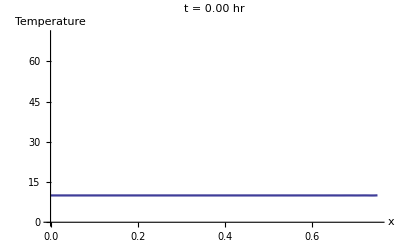

```mathematica
snapshot[0]
```

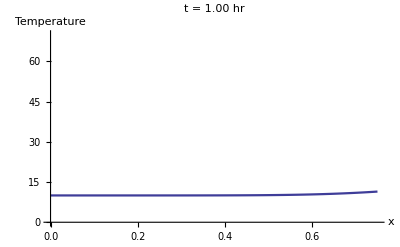

```mathematica
snapshot[1]
```

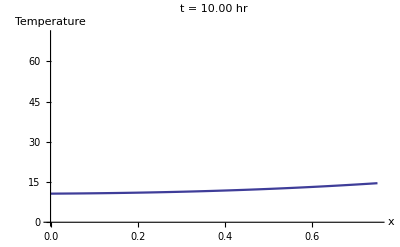

```mathematica
snapshot[10]
```

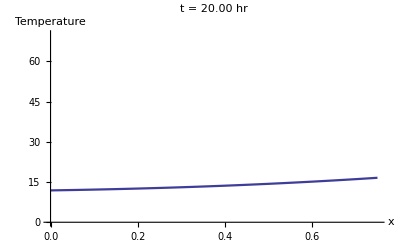

```mathematica
snapshot[20]
```

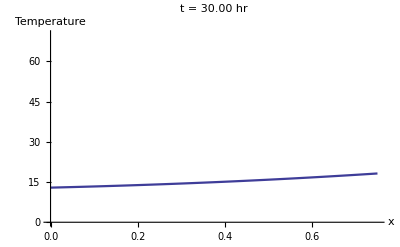

```mathematica
snapshot[30]
```

```mathematica
snapshotApprox[t_]:=Module[{time},time=3600*t;Plot[TempOneTermApprox[x,time],{x,0,L},PlotStyle->Thickness[0.004],PlotRange->plrange,AxesLabel->{"x","Temperature"},PlotLabel->Row[{"t = ",PaddedForm[t,{4,2}]," hr"}]]]
```

```mathematica
snapshotApprox[0]:=Plot[TempOneTermApprox[x,0],{x,0,L},PlotStyle->Thickness[0.004],PlotRange->plrange,AxesLabel->{"x","Temperature"},PlotLabel->Row[{"t = ",PaddedForm[0,{4,2}]," hr"}]]
```

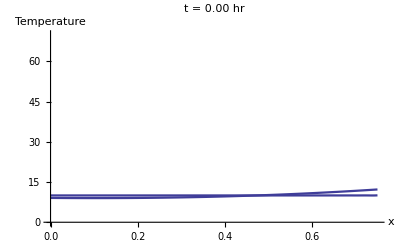

```mathematica
Show[snapshot[0],snapshotApprox[0]]
```

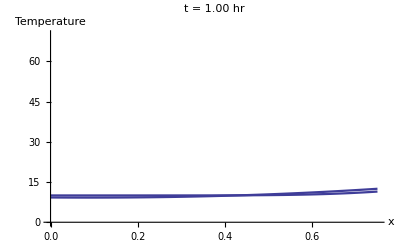

```mathematica
Show[snapshot[1],snapshotApprox[1]]
```

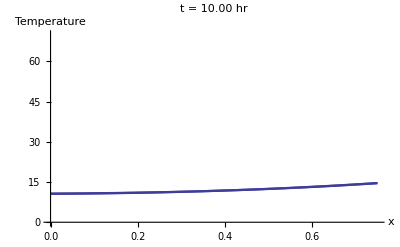

```mathematica
Show[snapshot[10],snapshotApprox[10]]
```

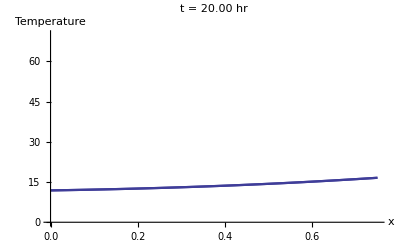

```mathematica
Show[snapshot[20],snapshotApprox[20]]
```

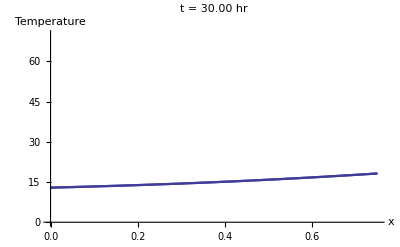

```mathematica
Show[snapshot[30],snapshotApprox[30]]
```

As a final task, we produce a sequence of 101 graphs that can be animated to show the dynamics of the heat loss process.  The graphs are at 0.5 hr intervals, running from 0 hr to 50 hr.  The graphs are output into a Manipulate panel for ease of viewing.

```mathematica
(* I changed the index in the following code from k to m *)
```

```mathematica
DynamicModule[{mangraph,i,k},Do[mangraph[i]=snapshot[0.5*i],{i,0,100}];Manipulate[mangraph[m],{m,0,100,1}]]
```